# An Introduction to Transmission Line Resonators

Let’s consider a scalar field ϕ(x,y) in the xy plane and define a vector field

The following electric and magnetic fields 

are guaranteed to satisfy the Maxwell equation, if the scalar field obeys the following partial differential equation, also called the 2D Laplace equation,

with associated boundary conditions provided that  k^2=ω^2/c^2. Solution of the 2D Laplace equation with attendant boundary conditions for the scalar potential is a common feature in electrostatics. Consider two parallel cylindrical conductors whose centers are separated by a distance 2a

```mathematica
ClearAll["Global`*"]
Graphics3D[{Cylinder[{{0,0,0},{0,10,0}},1/2],Cylinder[{{2,0,0},{2,10,0}},1/2]},Boxed->False]
```

-Graphics3D-

For two cylinders of radius r  separated by distance a, and held at constant potentials ±V0 the solution to the Laplace equation, in the region outside the cylinders is given by

```mathematica
v[x_,y_]=V0/(2 ArcCosh[a/r])Log[(y^2 + (x-√(a^2-r^2))^2)/(y^2 + (x+√(a^2-r^2))^2)]
```

(V0 Log[((-√(a^2-r^2)+x)^2+y^2)/((√(a^2-r^2)+x)^2+y^2)])/(2 ArcCosh[a/r])

And so the electric and magnetic, fields are given by

```mathematica
Efield[x_,y_,z_,t_]=-Append[FullSimplify[Grad[v[x,y],{x,y}]]ComplexExpand[Re[Exp[I ω/c z] Exp[I ω t]]],0]
Bfield[x_,y_,z_,t_]=FullSimplify[Cross[Efield[x,y,z,t],{0,0,1}]]
```

{-(2 √((a-r) (a+r)) V0 (-a^2+r^2+x^2-y^2) Cos[t ω+(z ω)/c])/(((-a^2+r^2+x^2)^2+2 (a^2-r^2+x^2) y^2+y^4) ArcCosh[a/r]),-(4 √((a-r) (a+r)) V0 x y Cos[t ω+(z ω)/c])/(((-a^2+r^2+x^2)^2+2 (a^2-r^2+x^2) y^2+y^4) ArcCosh[a/r]),0}

{-(4 √((a-r) (a+r)) V0 x y Cos[(t+z/c) ω])/(((-a^2+r^2+x^2)^2+2 (a^2-r^2+x^2) y^2+y^4) ArcCosh[a/r]),(2 √((a-r) (a+r)) V0 (-a^2+r^2+x^2-y^2) Cos[(t+z/c) ω])/(((-a^2+r^2+x^2)^2+2 (a^2-r^2+x^2) y^2+y^4) ArcCosh[a/r]),0}

```mathematica
(* for plotting purposes we initialize some parameters *)
(* c is the speed of light, ω is a frequency *)
c=1;r=1;a=3;V0=1;ω=2;
```

```mathematica
(* define plotting region *)
Ω=ImplicitRegion[(x-a)^2+y^2 ≥r^2 && (x+a)^2 +y^2 ≥r^2 && -10 < x <10 && -10 < y < 10,{x,y}];

figa=StreamPlot[{Efield[x,y,0,0][[1]],Efield[x,y,0,0][[2]]},{x,y}∈ Ω,StreamStyle->{Black},StreamPoints->40];
```

```mathematica
figb=StreamPlot[{Bfield[x,y,0,0][[1]],Bfield[x,y,0,0][[2]]},{x,y}∈ Ω,StreamStyle->{Red},StreamPoints->40];
```

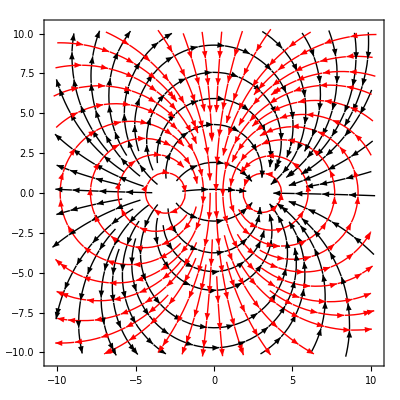

```mathematica
Show[figa,figb]
```

In the figure, above, we illustrate the stream lines, at t=0, and in the x,y plane at z=0, for the fields. The black lines correspond the  electric field, whereas the red to the magnetic field.

Construct the Poynting vector, defined in Eq. (8.4) of the text.

```mathematica
Poynt[x_,y_,z_,t_]=c/4/Pi Integrate[Cross[Efield[x,y,z,t],Bfield[x,y,z,t]],{t,0,2Pi/ω}]
```

{0,0,-4/((x^4+2 x^2 (-8+y^2)+(8+y^2)^2) ArcCosh[3]^2)}

```mathematica
g1=VectorPlot3D[Poynt[x,y,z,0],{x,-5,5},{y,-5,5},{z,-5,5},VectorStyle->{"Arrow3D",Red},VectorPoints->8,Axes->False,Boxed->False,RegionFunction->Function[{x,y},(x-a)^2+y^2 ≥r^2 && (x+a)^2 +y^2 ≥r^2]];
g2=Graphics3D[{Cylinder[{{-a,0,-5},{-a,0,5}},r],Cylinder[{{a,0,-5},{a,0,5}},r]},Boxed->False];
Show[g1,g2]
```

-Graphics3D-

In the figure above we show the poynting vector (red arrows)  corresponding to this wave guide. Its direction
determines the energy flow associated with the electromagnetic fields.

In the simulation below, we illustrate the propagation of the electromagnetic field as a function of time. 
The figure shows a series of discs that represents the waveguide cylinder cross sections, for different values of z,  along the waveguide axis (i.e. along the z-direction).

```mathematica
(* evector, bvector are the electric and megnetic vector fields, respectively, associcated with this wave gauide *)

evector[x_,y_,z_,t_]:=If[(x-a)^2+y^2>r ^2&& (x+a)^2+y^2>r^2,Arrow[{{x,y},{x+Efield[x,y,z,t][[1]],y+Efield[x,y,z,t][[2]]}}],Point[{x,y}]]

bvector[x_,y_,z_,t_]:=If[(x-a)^2+y^2>r ^2&& (x+a)^2+y^2>r^2,Arrow[{{x,y},{x+Bfield[x,y,z,t][[1]],y+Bfield[x,y,z,t][[2]]}}],Point[{x,y}]]
```

```mathematica
g[t_,z_]:=Graphics[{Black,Disk[{-a,0},r],Disk[{a,0},r],Arrowheads[0.02],Red,Table[evector[x,y,z,t],{x,-5,5,0.5},{y,-3,3}]},PlotRange->{{-5,5},{-3.2,3.2}}]
h[t_,z_]:=Graphics[{Arrowheads[0.02],Blue,Table[bvector[x,y,z,t],{x,-5,5,0.5},{y,-3,3}]},PlotRange->{{-5,5},{-3.2,3.2}}]
```

```mathematica
Manipulate[Table[Show[g[t,z],h[t,z]],{z,{0,ω/8,ω/4,3ω/8,4 ω/8,5ω/8,6ω/8,7 ω/8}}],{t,0,2Pi/ω,2Pi/ω/20},SaveDefinitions->True]
```

The  panels, illustrate how the transverse electric and magnetic fields propagate along the waveguide axis.